### init

```mathematica
basedir="D:\\data\\Cycle 198\\exp_3-16-19\\rawdata\\sc\\"
Get[basedir<>"..\\camera_ifg.m"]
minIntens=2000;  (* Schwellenwert zur Unterdrückung schwach beleuchtetet Randbereiche der Kamera *)
(*
loadimage[basedir<>filename]    liefert Array mit den einzelnen Bildern aus der Tiff-Datei.;
fittile[images_,tileDX_,tileDY_,nx_,ny_,minIntensity_,period_]

*)
```

D:\data\Cycle 198\exp_3-16-19\rawdata\sc\

```mathematica
LoadDatFile[filename_]:=  ToExpression[Transpose[StringSplit[#,"\t"] & /@ Pick[#,StringMatchQ[#,{"\\**","[*"," *","\t*",""}],False]&@Import[basedir<>filename,"lines"]]]
```

```mathematica
reduceSlotsBy[img_,its_,slotmax_]:=Module[{maxph,maxtim},
maxtim=slotmax/its;
maxph=Length[img]/(slotmax+2);
Flatten[Table[    Join[{img[[1+(ph-1)*(slotmax+2)]]},Table[Total[img[[(ph-1)*(slotmax+2)+1+(tim-1)*its;;(ph-1)*(slotmax+2)+tim*its]],1],{tim,1,maxtim}],{img[[ph*(slotmax+2)]]}]     ,{ph,1,maxph}],1]
]
```

```mathematica
(* alle Bilder eines Multi-Page-Images aufsummieren und auf die Anzahl der nicht leeren Pixel normieren *)
integrateImg[img_]:=(Total[#,2]&/@img)   / Count[Flatten[Total[img]],x_/;x>10]
(*integrateImg[img_]:=(Total[#,2]&/@img)   / (Length[img[[1]]]*Length[img[[1,1]]])*)
```

```mathematica
(* counts per pixel *)
cpp[img_]:=N[Total[img,2]  / (Times @@ Dimensions[img])];
```

# ...

```mathematica
filename = "ifg1_3p200s_22Sep1930.tif";
```

{31,55,50}

{0.548129,17434.3,10.0409}

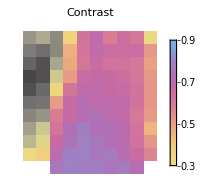
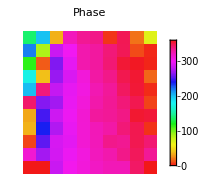
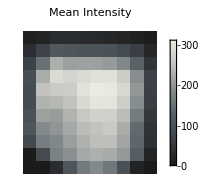
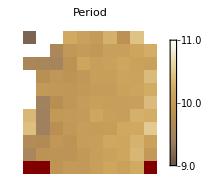

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]]}
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.1,+10];
plotres[res]
```

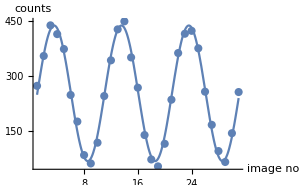
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 252.493 | 2.6484 | 95.3378 | 1.11866×10^-35
CameraIfgPackage`Private`b | 186.021 | 3.86518 | 48.1274 | 1.03622×10^-27
CameraIfgPackage`Private`c | 0.626683 | 0.00201338 | 311.26 | 1.54791×10^-49
CameraIfgPackage`Private`d | -0.64809 | 0.0365425 | -17.7353 | 2.09316×10^-16contr=0.736738
offs=252.493
phase=322.867°
period=10.0261

```mathematica
showtileres[res,5,3]
```

```mathematica
filename = "ifg2_3p200s_22Sep2123.tif";
```

{31,55,50}

{0.556244,17444.3,11.7822}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

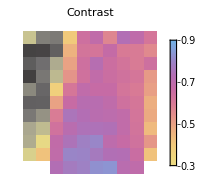
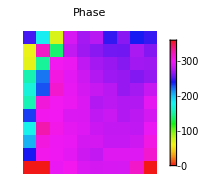
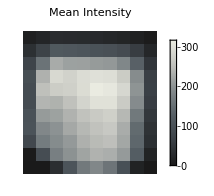
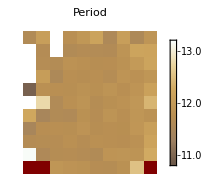

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,1.2,+12];
plotres[res]
```

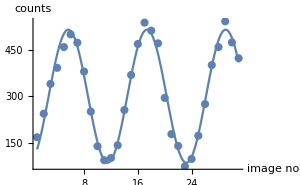
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 300.412 | 4.64205 | 64.7154 | 3.7331×10^-31
CameraIfgPackage`Private`b | 214.568 | 6.51632 | 32.9277 | 2.46739×10^-23
CameraIfgPackage`Private`c | 0.536701 | 0.00307093 | 174.768 | 8.9985×10^-43
CameraIfgPackage`Private`d | -1.46404 | 0.0558582 | -26.2099 | 9.74614×10^-21contr=0.714245
offs=300.412
phase=276.117°
period=11.707

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg1_3p200s_23Sep0303.tif";
```

{31,55,50}

{0.530367,17083.6,10.1623}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

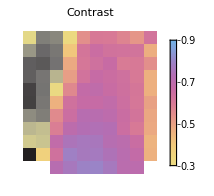
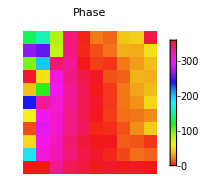
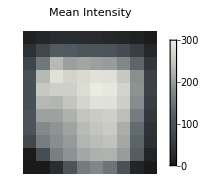
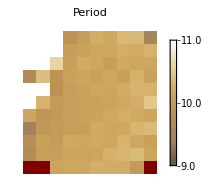

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]]}
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,9][[3;;5]]
res=fitgrid[img,5,5,1.1,+10];
plotres[res]
```

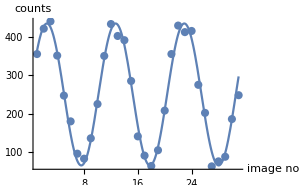
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 249.936 | 4.00989 | 62.33 | 1.0224×10^-30
CameraIfgPackage`Private`b | 184.423 | 5.72528 | 32.212 | 4.40294×10^-23
CameraIfgPackage`Private`c | 0.614725 | 0.00321044 | 191.477 | 7.66199×10^-44
CameraIfgPackage`Private`d | 0.0502877 | 0.0595276 | 0.84478 | 0.405657contr=0.737879
offs=249.936
phase=2.88127°
period=10.2211

```mathematica
showtileres[res,5,3]
```

```mathematica
filename = "ifg1_3p200s_23Sep0854.tif";
```

{31,60,50}

{0.576383,22054.8,10.1384}

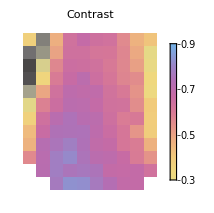
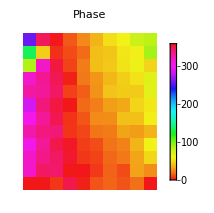
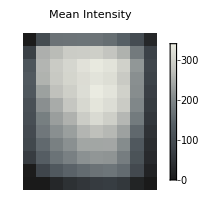
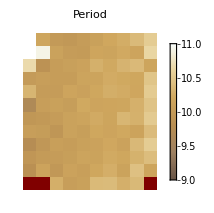

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

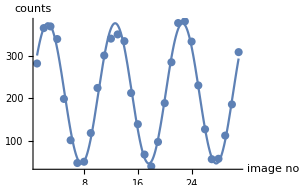
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 212.181 | 2.96332 | 71.6023 | 2.47104×10^-32
CameraIfgPackage`Private`b | 166.268 | 4.25769 | 39.0512 | 2.70493×10^-25
CameraIfgPackage`Private`c | 0.62665 | 0.00253007 | 247.681 | 7.38007×10^-47
CameraIfgPackage`Private`d | -0.0565981 | 0.0474454 | -1.19291 | 0.243282contr=0.783615
offs=212.181
phase=356.757°
period=10.0266

```mathematica
showtileres[res,3,3]
```

```mathematica
filename = "ifg2_3p200s_B1_23Sep1203.tif";
```

{31,60,50}

{0.184733,20359.4,11.8131}

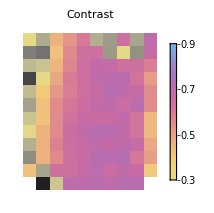
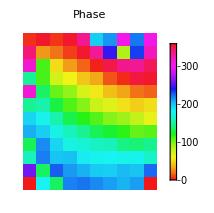
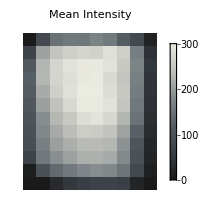
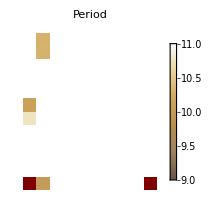

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

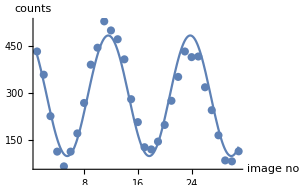
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 289.926 | 7.15612 | 40.5144 | 1.0182×10^-25
CameraIfgPackage`Private`b | 191.987 | 10.2526 | 18.7256 | 5.36924×10^-17
CameraIfgPackage`Private`c | 0.514851 | 0.00583496 | 88.2356 | 8.98817×10^-35
CameraIfgPackage`Private`d | 1.88301 | 0.0997097 | 18.885 | 4.33882×10^-17contr=0.662194
offs=289.926
phase=107.889°
period=12.2039

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg2_3p200s_B1_23Sep1406.tif";
```

{31,60,50}

{0.192583,22347.3,11.6619}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

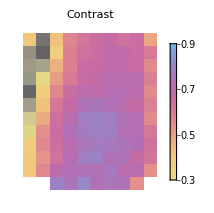
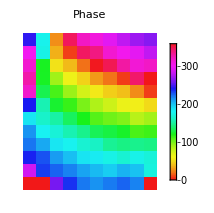
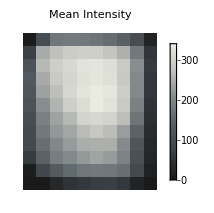
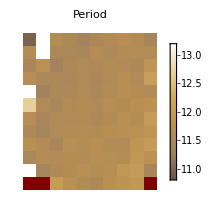

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

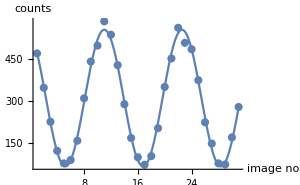
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 309.987 | 3.17977 | 97.4873 | 6.13756×10^-36
CameraIfgPackage`Private`b | -244.81 | 4.63253 | -52.846 | 8.50873×10^-29
CameraIfgPackage`Private`c | 0.543044 | 0.00188252 | 288.466 | 1.20578×10^-48
CameraIfgPackage`Private`d | 1.87774 | 0.0339681 | 55.2795 | 2.55041×10^-29contr=0.789744
offs=309.987
phase=107.587°
period=11.5703

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg2_3p120s_B1_23Sep1707.tif";
```

{21,60,50}

{0.332159,13756.4,11.2298}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit :: cvmit will be suppressed during this calculation.

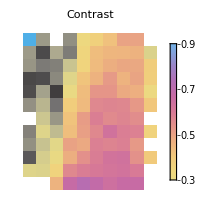
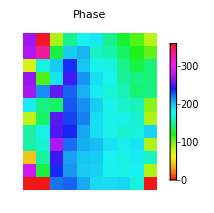
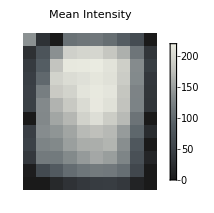
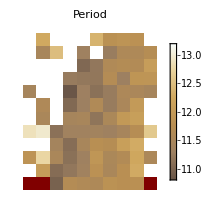

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

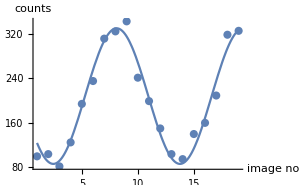
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 207.978 | 4.53122 | 45.8988 | 1.50862×10^-17
CameraIfgPackage`Private`b | 121.518 | 6.08913 | 19.9566 | 3.25618×10^-12
CameraIfgPackage`Private`c | 0.555575 | 0.0102997 | 53.941 | 1.35767×10^-18
CameraIfgPackage`Private`d | -2.93451 | 0.118646 | -24.7333 | 1.42511×10^-13contr=0.584285
offs=207.978
phase=191.865°
period=11.3093

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg2_3p200s_B1_24Sep0018.tif";
```

{31,60,50}

{0.38171,23422.,11.7186}

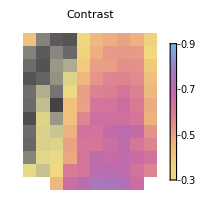
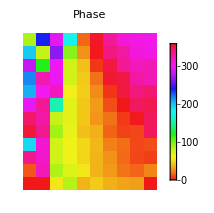
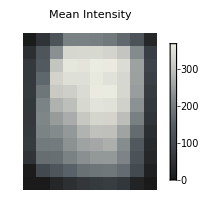
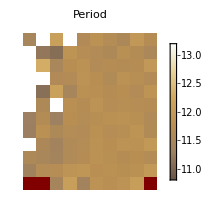

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

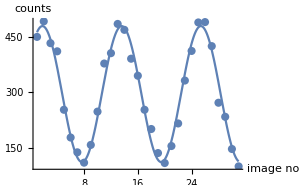
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 294.425 | 4.62441 | 63.6676 | 5.78445×10^-31
CameraIfgPackage`Private`b | 183.72 | 6.36 | 28.8867 | 7.70056×10^-22
CameraIfgPackage`Private`c | 0.533088 | 0.0040318 | 132.221 | 1.66653×10^-39
CameraIfgPackage`Private`d | 0.609805 | 0.0734602 | 8.30116 | 6.5558×10^-9contr=0.623994
offs=294.425
phase=34.9393°
period=11.7864

```mathematica
showtileres[res,5,4]
```

```mathematica
filename = "ifg1_3p200s_B2_24Sep0211.tif";
```

{31,60,50}

{0.522975,20137.8,9.88247}

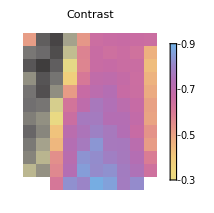
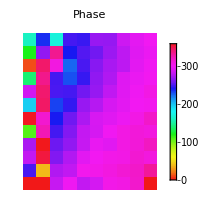
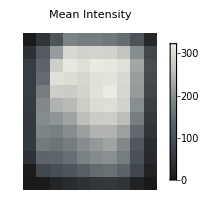
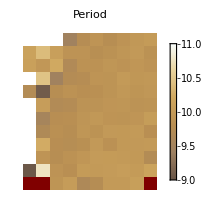

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

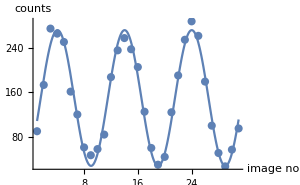
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 149.543 | 2.78289 | 53.7367 | 5.4406×10^-29
CameraIfgPackage`Private`b | 121.636 | 4.00658 | 30.3589 | 2.0915×10^-22
CameraIfgPackage`Private`c | 0.629104 | 0.0033664 | 186.877 | 1.47651×10^-43
CameraIfgPackage`Private`d | -0.974602 | 0.0597722 | -16.3053 | 1.67953×10^-15contr=0.813381
offs=149.543
phase=304.159°
period=9.98751

```mathematica
showtileres[res,5,1]
```

```mathematica
filename = "ifg2_3p200s_B2_24Sep0402.tif";
```

{31,60,50}

{0.516683,20272.5,11.8011}

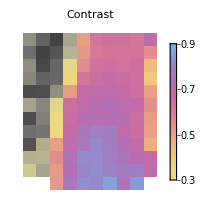
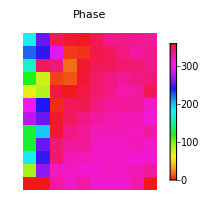
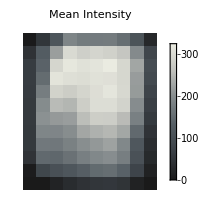
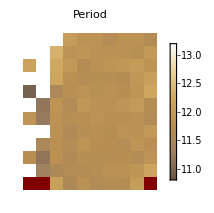

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

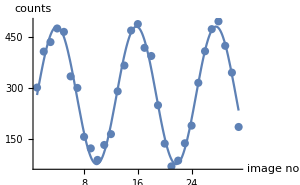
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 279.116 | 4.3938 | 63.5251 | 6.14299×10^-31
CameraIfgPackage`Private`b | 202.464 | 6.28273 | 32.2255 | 4.35484×10^-23
CameraIfgPackage`Private`c | 0.530871 | 0.00288706 | 183.879 | 2.28419×10^-43
CameraIfgPackage`Private`d | -0.526186 | 0.0534517 | -9.84415 | 1.98666×10^-10contr=0.725375
offs=279.116
phase=329.852°
period=11.8356

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg1_3p200s_B3_24Sep0555.tif";
```

{31,60,50}

{0.621718,26577.8,9.99412}

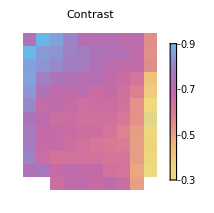
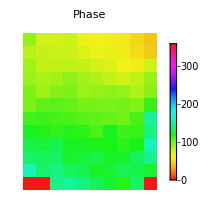
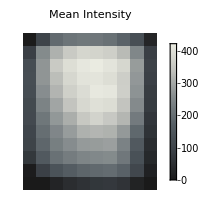
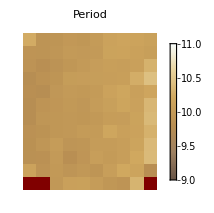

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

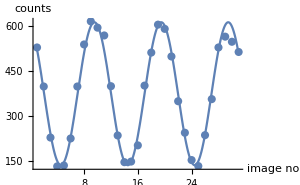
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 373.928 | 4.50567 | 82.9905 | 4.67444×10^-34
CameraIfgPackage`Private`b | -237.952 | 6.43119 | -36.9997 | 1.13174×10^-24
CameraIfgPackage`Private`c | 0.630734 | 0.00276892 | 227.791 | 7.06694×10^-46
CameraIfgPackage`Private`d | 1.84396 | 0.0498293 | 37.0055 | 1.12705×10^-24contr=0.636357
offs=373.928
phase=105.651°
period=9.96171

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg2_3p120s_B1_24Sep1642.tif";
```

{19,60,50}

{0.501985,11530.6,11.6848}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

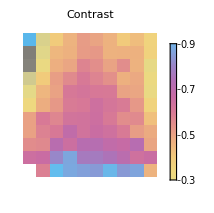
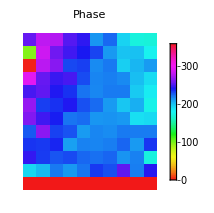
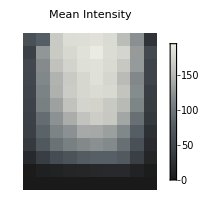
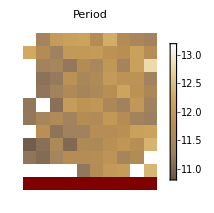

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

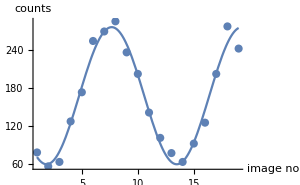
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 167.576 | 3.96451 | 42.2691 | 5.1449×10^-17
CameraIfgPackage`Private`b | 108.241 | 5.34842 | 20.2379 | 2.65816×10^-12
CameraIfgPackage`Private`c | 0.540644 | 0.010229 | 52.8541 | 1.83972×10^-18
CameraIfgPackage`Private`d | -2.57365 | 0.117606 | -21.8836 | 8.53123×10^-13contr=0.64592
offs=167.576
phase=212.541°
period=11.6217

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg2_3p120s_B2_24Sep1926.tif";
```

{31,60,50}

{0.527341,11545.1,11.6518}

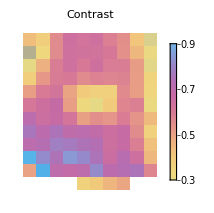
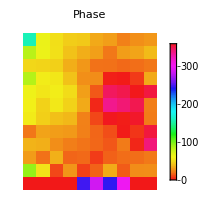
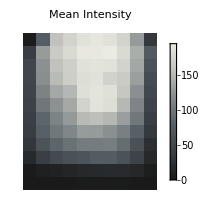
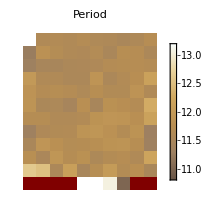

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

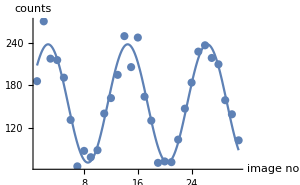
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 154.379 | 3.42869 | 45.0257 | 6.12817×10^-27
CameraIfgPackage`Private`b | 83.9791 | 4.78905 | 17.5356 | 2.7752×10^-16
CameraIfgPackage`Private`c | 0.530786 | 0.00608912 | 87.1697 | 1.24654×10^-34
CameraIfgPackage`Private`d | 0.166115 | 0.114901 | 1.44573 | 0.159761contr=0.54398
offs=154.379
phase=9.51771°
period=11.8375

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg2_3p120s_B1_25Sep0055.tif";
```

{31,60,50}

{0.358247,12688.6,11.7572}

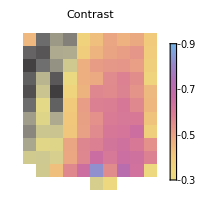
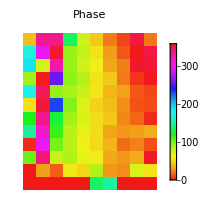
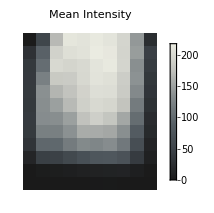
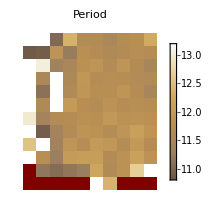

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

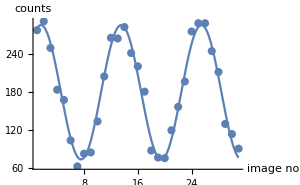
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 179.05 | 2.66571 | 67.1678 | 1.37567×10^-31
CameraIfgPackage`Private`b | 106.003 | 3.67798 | 28.8211 | 8.17325×10^-22
CameraIfgPackage`Private`c | 0.526204 | 0.00401859 | 130.942 | 2.16557×10^-39
CameraIfgPackage`Private`d | 0.742523 | 0.0744344 | 9.97552 | 1.49645×10^-10contr=0.59203
offs=179.05
phase=42.5434°
period=11.9406

```mathematica
showtileres[res,6,5]
```

```mathematica
filename = "ifg1_3p120s_B2_25Sep0207.tif";
```

{31,60,50}

{0.15725,44.6409,9.72048}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

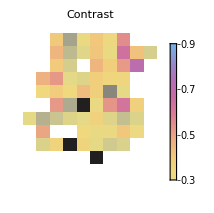
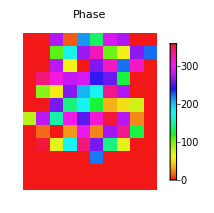
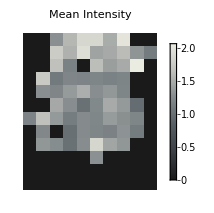
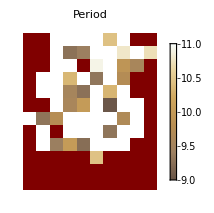

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

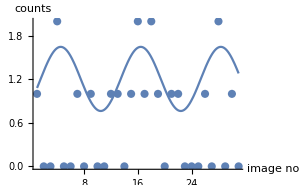
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 1.20598 | 0.112949 | 10.6771 | 1.75656×10^-7
CameraIfgPackage`Private`b | 0.44201 | 0.1517 | 2.91371 | 0.0129911
CameraIfgPackage`Private`c | 0.527371 | 0.0421252 | 12.5192 | 3.01251×10^-8
CameraIfgPackage`Private`d | 5.47026 | 0.718354 | 7.61499 | 6.20686×10^-6contr=0.366516
offs=1.20598
phase=313.423°
period=11.9142

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg2_3p120s_B2_25Sep0317.tif";
```

{31,60,50}

{0.45587,10578.,11.4833}

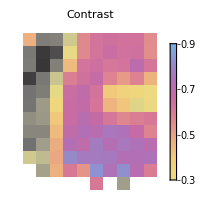
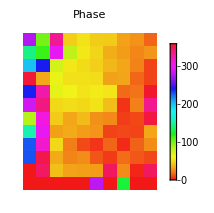
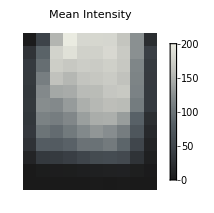
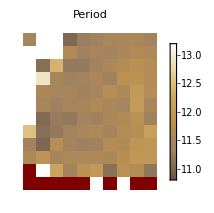

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

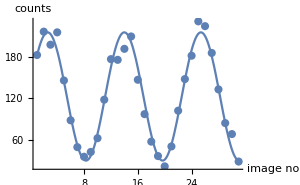
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 122.693 | 2.74356 | 44.7206 | 7.34583×10^-27
CameraIfgPackage`Private`b | 93.2603 | 3.80679 | 24.4984 | 5.62111×10^-20
CameraIfgPackage`Private`c | 0.55121 | 0.00444197 | 124.091 | 9.21999×10^-39
CameraIfgPackage`Private`d | 0.145347 | 0.0803328 | 1.80931 | 0.0815513contr=0.760108
offs=122.693
phase=8.32775°
period=11.3989

```mathematica
showtileres[res,6,4]
```

```mathematica
filename = "ifg1_3p120s_B3_25Sep0428.tif";
```

{31,60,50}

{0.620707,14191.2,9.98043}

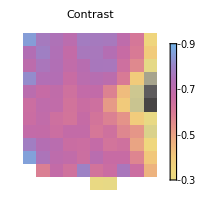
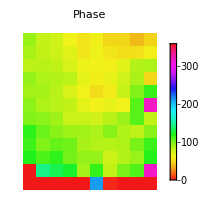
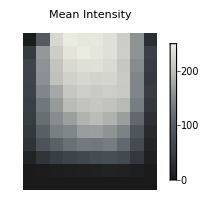
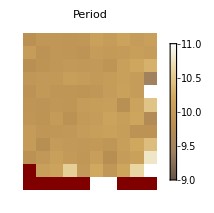

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

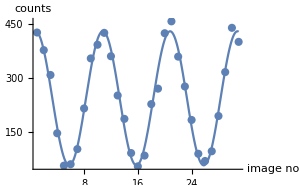
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 244.136 | 4.49075 | 54.3643 | 3.98753×10^-29
CameraIfgPackage`Private`b | 186.166 | 6.12283 | 30.4053 | 2.00938×10^-22
CameraIfgPackage`Private`c | 0.627421 | 0.00374904 | 167.355 | 2.89692×10^-42
CameraIfgPackage`Private`d | 1.08467 | 0.0670712 | 16.1719 | 2.05514×10^-15contr=0.762551
offs=244.136
phase=62.147°
period=10.0143

```mathematica
showtileres[res,5,10]
```

```mathematica
filename = "ifg1_3p120s_B2_25Sep0922.tif";
```

{30,60,50}

{0.506239,13456.8,10.4573}

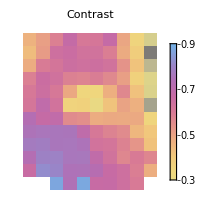
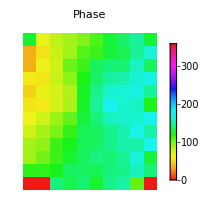
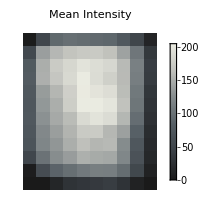
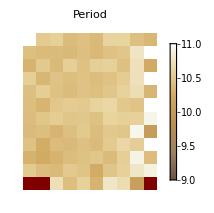

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

```mathematica
showtileres[res,5,10]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 244.136 | 4.49075 | 54.3643 | 3.98753×10^-29
CameraIfgPackage`Private`b | 186.166 | 6.12283 | 30.4053 | 2.00938×10^-22
CameraIfgPackage`Private`c | 0.627421 | 0.00374904 | 167.355 | 2.89692×10^-42
CameraIfgPackage`Private`d | 1.08467 | 0.0670712 | 16.1719 | 2.05514×10^-15contr=0.762551
offs=244.136
phase=62.147°
period=10.0143

```mathematica
filename = "ifg2_3p120s_B1_25Sep1045.tif";
```

{31,60,50}

{0.549047,15111.4,12.0597}

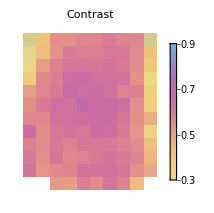
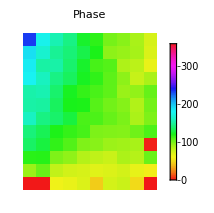
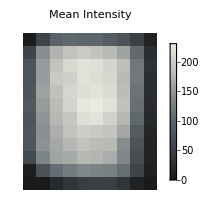
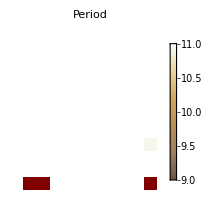

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

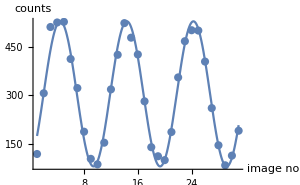
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 304.082 | 4.62947 | 65.684 | 2.50568×10^-31
CameraIfgPackage`Private`b | 224.4 | 6.62994 | 33.8464 | 1.19378×10^-23
CameraIfgPackage`Private`c | 0.634092 | 0.00309546 | 204.845 | 1.24023×10^-44
CameraIfgPackage`Private`d | -1.25359 | 0.0547675 | -22.8894 | 3.24382×10^-19contr=0.737959
offs=304.082
phase=288.174°
period=9.90895

```mathematica
showtileres[res,6,6]
```

```mathematica
filename = "ifg1_3p120s_B2_25Sep0922.tif";
```

{31,60,50}

{0.499867,13388.1,10.4299}

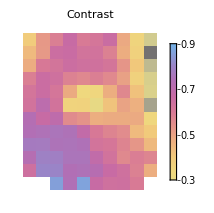
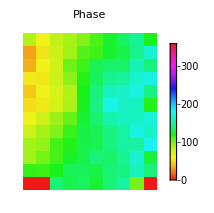
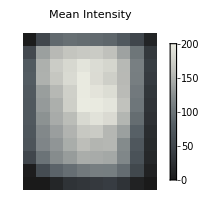
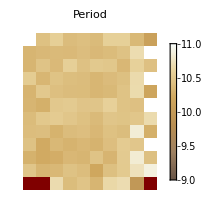

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

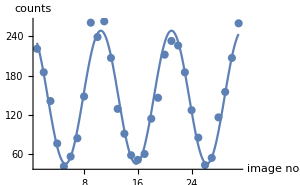
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 146.825 | 3.46487 | 42.3753 | 3.08401×10^-26
CameraIfgPackage`Private`b | 101.845 | 4.82946 | 21.0883 | 2.6476×10^-18
CameraIfgPackage`Private`c | 0.597211 | 0.00501933 | 118.982 | 2.86313×10^-38
CameraIfgPackage`Private`d | 1.58789 | 0.0905243 | 17.5411 | 2.75384×10^-16contr=0.693649
offs=146.825
phase=90.9796°
period=10.5209

```mathematica
showtileres[res,2,5]
```

```mathematica
filename = "ifg1_3p120s_B3_25Sep1150.tif";
```

{31,60,50}

{0.445462,16710.3,10.0496}

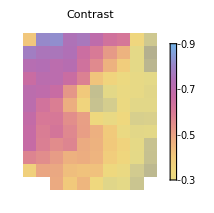
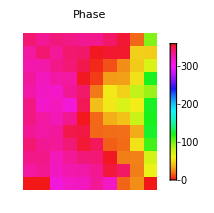
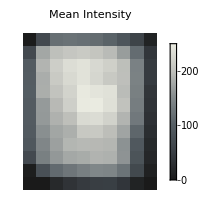
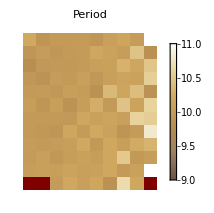

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

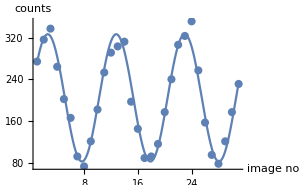
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 204.318 | 3.34595 | 61.0642 | 1.77242×10^-30
CameraIfgPackage`Private`b | 121.939 | 4.77829 | 25.5194 | 1.95065×10^-20
CameraIfgPackage`Private`c | 0.616598 | 0.00408538 | 150.928 | 4.70077×10^-41
CameraIfgPackage`Private`d | -0.0280566 | 0.0765831 | -0.366354 | 0.716956contr=0.59681
offs=204.318
phase=358.392°
period=10.1901

```mathematica
showtileres[res,5,10]
```

```mathematica
filename = "ifg1_3p120s_B2_25Sep1545.tif";
```

```mathematica
(* after cleaning *)
```

{17,60,50}

{0.515,13751.2,10.0976}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

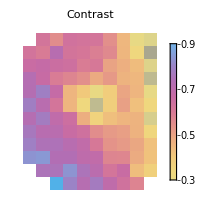
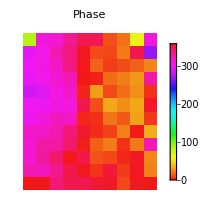
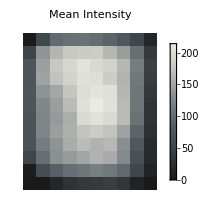
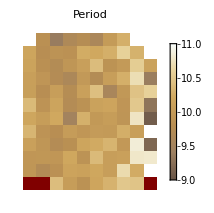

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

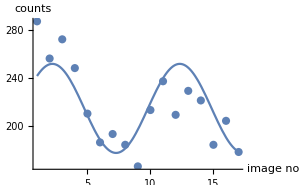
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 214.367 | 6.20911 | 34.5246 | 3.57279×10^-14
CameraIfgPackage`Private`b | 37.1446 | 8.28082 | 4.48561 | 0.000613233
CameraIfgPackage`Private`c | 0.621385 | 0.0501415 | 12.3926 | 1.41899×10^-8
CameraIfgPackage`Private`d | 0.192914 | 0.505621 | 0.381539 | 0.708966contr=0.173276
offs=214.367
phase=11.0532°
period=10.1116

```mathematica
showtileres[res,5,6]
```

```mathematica
filename = "ifg1_3p120s_B2_25Sep1746.tif";
```

```mathematica
(* after cleaning *)
```

{13,60,50}

{0.408804,11836.3,8.91723}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit :: cvmit will be suppressed during this calculation.

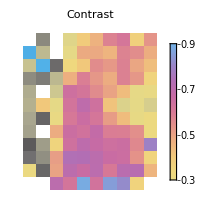
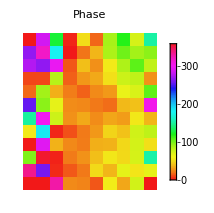
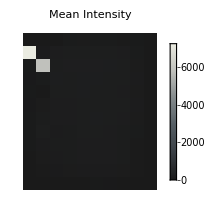
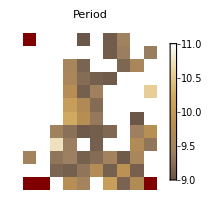

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

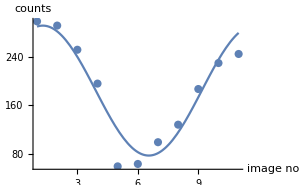
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 184.419 | 13.1264 | 14.0495 | 2.19306×10^-6
CameraIfgPackage`Private`b | 107.492 | 11.9604 | 8.98734 | 0.0000430494
CameraIfgPackage`Private`c | 0.59773 | 0.0591278 | 10.1091 | 0.0000199163
CameraIfgPackage`Private`d | 0.801359 | 0.39383 | 2.03478 | 0.0813365contr=0.58287
offs=184.419
phase=45.9145°
period=10.5117

```mathematica
showtileres[res,5,5]
```

```mathematica
filename = "ifg2_3p120s_B1_25Sep2027.tif";
```

{31,60,50}

{0.431875,12754.4,11.6422}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

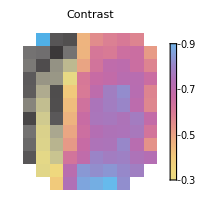
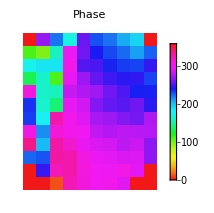
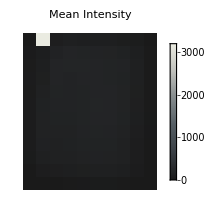
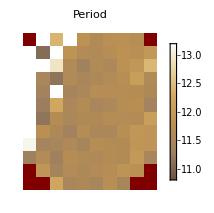

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,300,+12];
plotres[res]
```

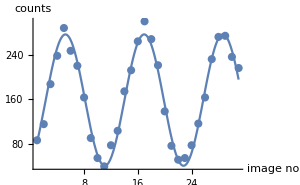
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 158.284 | 2.72319 | 58.1245 | 6.65094×10^-30
CameraIfgPackage`Private`b | 118.164 | 3.84454 | 30.7356 | 1.51282×10^-22
CameraIfgPackage`Private`c | 0.536086 | 0.00317933 | 168.616 | 2.36595×10^-42
CameraIfgPackage`Private`d | -1.22804 | 0.0587815 | -20.8916 | 3.36217×10^-18contr=0.746534
offs=158.284
phase=289.639°
period=11.7205

```mathematica
showtileres[res,5,3]
```

```mathematica
filename = "ifg1_3p120s_B2_25Sep2139.tif";
```

{31,60,50}

{0.474549,11429.2,10.0769}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

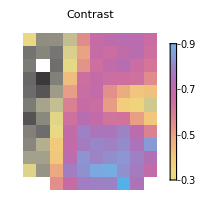
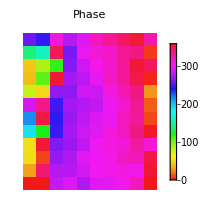
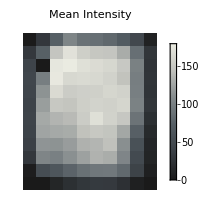
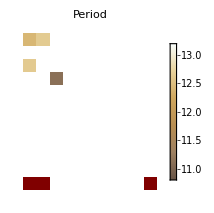

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

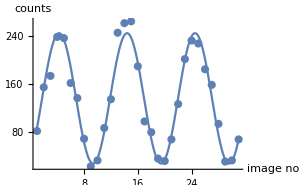
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 135.508 | 3.60922 | 37.545 | 7.67944×10^-25
CameraIfgPackage`Private`b | 108.722 | 5.12932 | 21.1962 | 2.32431×10^-18
CameraIfgPackage`Private`c | 0.621089 | 0.00493253 | 125.917 | 6.21942×10^-39
CameraIfgPackage`Private`d | -1.08789 | 0.0863585 | -12.5974 | 8.10019×10^-13contr=0.802329
offs=135.508
phase=297.669°
period=10.1164

```mathematica
showtileres[res,5,3]
```

```mathematica
filename = "ifg2_3p120s_B2_25Sep2249.tif";
```

{31,60,50}

{0.480711,11591.,11.8278}

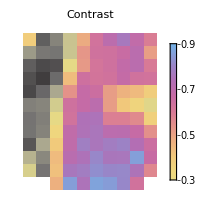
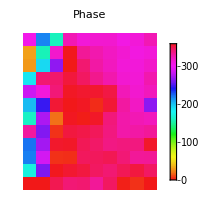
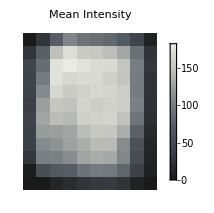
-Graphics--Graphics--Graphics--Graphics-

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

```mathematica
showtileres[res,5,3]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 142.322 | 4.33422 | 32.8367 | 2.65418×10^-23
CameraIfgPackage`Private`b | 107.802 | 6.1771 | 17.4519 | 3.12612×10^-16
CameraIfgPackage`Private`c | 0.5309 | 0.0053567 | 99.1095 | 3.93544×10^-36
CameraIfgPackage`Private`d | -0.282269 | 0.0996517 | -2.83256 | 0.00862548contr=0.757456
offs=142.322
phase=343.827°
period=11.835

```mathematica
filename = "ifg1_3p120s_B3_26Sep0002.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.60781,15117.7,9.93777}

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,3]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 176.925 | 2.95946 | 59.7828 | 3.12961×10^-30
CameraIfgPackage`Private`b | 116.059 | 4.26838 | 27.1904 | 3.74443×10^-21
CameraIfgPackage`Private`c | 0.628439 | 0.00369008 | 170.305 | 1.8082×10^-42
CameraIfgPackage`Private`d | -0.361685 | 0.068243 | -5.29996 | 0.000013616contr=0.655978
offs=176.925
phase=339.277°
period=9.99809

```mathematica
filename = "ifg2_3p120s_B1_26Sep0113.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.405509,13099.,11.7647}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,3]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 162.001 | 3.28784 | 49.2727 | 5.52923×10^-28
CameraIfgPackage`Private`b | 110.591 | 4.63541 | 23.8578 | 1.11494×10^-19
CameraIfgPackage`Private`c | 0.545661 | 0.00420734 | 129.693 | 2.80452×10^-39
CameraIfgPackage`Private`d | -1.48453 | 0.0783812 | -18.9398 | 4.0332×10^-17contr=0.682656
offs=162.001
phase=274.943°
period=11.5148

```mathematica
filename = "ifg1_3p120s_B2_26Sep0225.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.491672,11315.8,10.0895}

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,3]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 131.45 | 2.73053 | 48.1407 | 1.02859×10^-27
CameraIfgPackage`Private`b | 105.894 | 3.96251 | 26.7241 | 5.87776×10^-21
CameraIfgPackage`Private`c | 0.624984 | 0.00375138 | 166.601 | 3.27228×10^-42
CameraIfgPackage`Private`d | -0.913754 | 0.0654072 | -13.9702 | 7.10478×10^-14contr=0.805589
offs=131.45
phase=307.646°
period=10.0534

```mathematica
filename = "ifg2_3p120s_B2_26Sep0336.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.43183,11667.6,11.8761}

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,3]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 139.123 | 3.10541 | 44.8003 | 7.00501×10^-27
CameraIfgPackage`Private`b | 106.755 | 4.43749 | 24.0576 | 8.98871×10^-20
CameraIfgPackage`Private`c | 0.533803 | 0.00380471 | 140.3 | 3.36737×10^-40
CameraIfgPackage`Private`d | -0.5492 | 0.0705627 | -7.78315 | 2.2748×10^-8contr=0.767343
offs=139.123
phase=328.533°
period=11.7706

```mathematica
filename = "ifg1_3p120s_B3_26Sep0448.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.650044,14692.,9.95408}

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,3]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 164.397 | 3.08234 | 53.3353 | 6.64929×10^-29
CameraIfgPackage`Private`b | -109.498 | 4.36934 | -25.0605 | 3.1233×10^-20
CameraIfgPackage`Private`c | 0.62933 | 0.00416443 | 151.12 | 4.54203×10^-41
CameraIfgPackage`Private`d | 0.0421757 | 0.0770892 | 0.547103 | 0.588802contr=0.666058
offs=164.397
phase=2.41649°
period=9.98393

```mathematica
filename = "ifg2_3p120s_B1_26Sep0600.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.400441,13287.3,11.6842}

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,3]
```

```mathematica
filename = "ifg2_3p200s_B1_27Sep2010.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.646997,2610.22,11.7046}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,6,3]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 206.045 | 2.31141 | 89.1427 | 6.82545×10^-35
CameraIfgPackage`Private`b | -136.586 | 3.39438 | -40.2388 | 1.22068×10^-25
CameraIfgPackage`Private`c | 0.536839 | 0.00245257 | 218.888 | 2.07229×10^-45
CameraIfgPackage`Private`d | 2.57354 | 0.0457887 | 56.2048 | 1.6353×10^-29contr=0.662892
offs=206.045
phase=147.453°
period=11.704

```mathematica
filename = "ifg2_3p200s_B2_27Sep2205.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.757817,2231.84,11.8027}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,2]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 153.37 | 2.51268 | 61.0384 | 1.7926×10^-30
CameraIfgPackage`Private`b | 122.132 | 3.50985 | 34.7969 | 5.74373×10^-24
CameraIfgPackage`Private`c | 0.531003 | 0.0032195 | 164.933 | 4.29236×10^-42
CameraIfgPackage`Private`d | 0.978152 | 0.0581674 | 16.8162 | 7.8477×10^-16contr=0.796323
offs=153.37
phase=56.044°
period=11.8327

```mathematica
filename = "ifg1_3p200s_B2_28Sep0000.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

{31,60,50}

{0.788159,2185.96,10.0319}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,2]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 145.249 | 3.35781 | 43.2569 | 1.78258×10^-26
CameraIfgPackage`Private`b | 119.103 | 4.63488 | 25.6972 | 1.62888×10^-20
CameraIfgPackage`Private`c | 0.624668 | 0.00442785 | 141.077 | 2.90161×10^-40
CameraIfgPackage`Private`d | -2.3653 | 0.0810193 | -29.1943 | 5.83496×10^-22contr=0.819996
offs=145.249
phase=224.478°
period=10.0584

```mathematica
filename = "ifg1_3p200s_B3_28Sep0156.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+10];
plotres[res]
```

{31,60,50}

{0.615215,2740.04,10.0349}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,4]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 245.9 | 3.38513 | 72.6412 | 1.6781×10^-32
CameraIfgPackage`Private`b | -153.393 | 4.7322 | -32.4147 | 3.73248×10^-23
CameraIfgPackage`Private`c | 0.538067 | 0.00351846 | 152.927 | 3.29645×10^-41
CameraIfgPackage`Private`d | 1.40551 | 0.0622555 | 22.5764 | 4.62104×10^-19contr=0.623802
offs=245.9
phase=80.5297°
period=11.6773

```mathematica
filename = "ifg2_3p200s_28Sep0351.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.609843,3411.15,11.7467}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,2]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 193.515 | 3.46924 | 55.7802 | 2.00344×10^-29
CameraIfgPackage`Private`b | -127.636 | 4.94743 | -25.7984 | 1.47063×10^-20
CameraIfgPackage`Private`c | 0.53491 | 0.00416786 | 128.342 | 3.7193×10^-39
CameraIfgPackage`Private`d | 1.69047 | 0.0738728 | 22.8834 | 3.26552×10^-19contr=0.659567
offs=193.515
phase=96.8565°
period=11.7463

```mathematica
filenamefilename = "ifg1_3p200s_28Sep0545.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.609843,3411.15,11.7467}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,2]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 193.515 | 3.46924 | 55.7802 | 2.00344×10^-29
CameraIfgPackage`Private`b | -127.636 | 4.94743 | -25.7984 | 1.47063×10^-20
CameraIfgPackage`Private`c | 0.53491 | 0.00416786 | 128.342 | 3.7193×10^-39
CameraIfgPackage`Private`d | 1.69047 | 0.0738728 | 22.8834 | 3.26552×10^-19contr=0.659567
offs=193.515
phase=96.8565°
period=11.7463

```mathematica
filenamefilename ="ifg2_3p120s_B1_28Sep1531.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,10,+12];
plotres[res]
```

{31,60,50}

{0.609843,3411.15,11.7467}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,2]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 193.515 | 3.46924 | 55.7802 | 2.00344×10^-29
CameraIfgPackage`Private`b | -127.636 | 4.94743 | -25.7984 | 1.47063×10^-20
CameraIfgPackage`Private`c | 0.53491 | 0.00416786 | 128.342 | 3.7193×10^-39
CameraIfgPackage`Private`d | 1.69047 | 0.0738728 | 22.8834 | 3.26552×10^-19contr=0.659567
offs=193.515
phase=96.8565°
period=11.7463

```mathematica
filename = "ifg1_newPS_2p120s_B3_06Oct1208.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,50,10];
plotres[res]
```

{30,60,50}

{0.62873,9502.24,9.94082}

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,2]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 70.6125 | 2.94063 | 24.0127 | 5.61292×10^-14
CameraIfgPackage`Private`b | 65.9343 | 4.23732 | 15.5604 | 4.40282×10^-11
CameraIfgPackage`Private`c | 0.642088 | 0.00969564 | 66.2244 | 5.99546×10^-21
CameraIfgPackage`Private`d | -0.267744 | 0.115296 | -2.32223 | 0.0337363contr=0.933749
offs=70.6125
phase=344.659°
period=9.78556

```mathematica
filename = "ifg2_newPS_3p120s_B2_06Oct1340.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
totalres=fitarea[img,0,0,Length[img[[1,1]]], Length[img[[1]]] ,1,11][[3;;5]]
res=fitgrid[img,5,5,70,9.7];
plotres[res]
```

{30,60,50}

```mathematica
{0.5574526645182191,7399.456799995986
,9.795269924014068}
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
showtileres[res,5,5]
```

-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 110.389 | 2.92446 | 37.7469 | 3.07298×10^-24
CameraIfgPackage`Private`b | 90.0187 | 4.22428 | 21.3098 | 5.4793×10^-18
CameraIfgPackage`Private`c | 0.650423 | 0.00472522 | 137.649 | 9.31856×10^-39
CameraIfgPackage`Private`d | -0.215538 | 0.08499 | -2.53604 | 0.0175605contr=0.815465
offs=110.389
phase=347.651°
period=9.66015